```mathematica
A[x_]:=Piecewise[{{0.1, 1≤x<3}, {0.5*(x-1),3≤x≤5}}];
b[x_]:=FullSimplify[Piecewise[{{10, 1≤x<3}, {0,3≤x≤5}}] ];
```

```mathematica
innerIntegral[r_]:= FullSimplify[Integrate[b[s],{s,1,r},Assumptions->1<r<5]+150*HeavisideTheta[r-3]];
```

```mathematica
c1 =FullSimplify[ NIntegrate[-1/(20*10^6*A[r])*innerIntegral[r],{r,5,1}]/NIntegrate[0.1/A[s],{s,5,1}]]
```

-0.0000101857

```mathematica
usol[x_]:=FullSimplify[-Integrate[1/(20*10^6*A[r])*innerIntegral[r],{r,5,x},Assumptions->1≤x≤5]+c1*Integrate[1/A[s],{s,5,x},Assumptions->1≤x≤5]];
```

```mathematica
ue = FullSimplify[usol[x]];
```

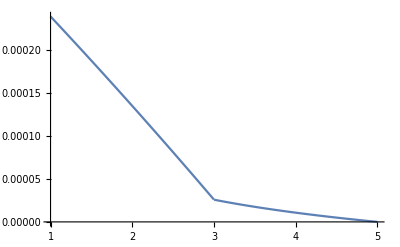

```mathematica
Plot[ue,{x,1,5}]
```

```mathematica
inn = innerIntegral[x];
```

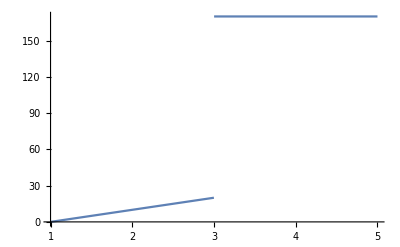

```mathematica
Plot[inn,{x,1,5}]
```